## This notebook accompanies the paper by Vinton and Vasseur titled “Resource limitation determines realized thermal performance of consumers in trophodynamic models. ”

### Define the Model Equation and functions governing consumer dynamics

```mathematica
(* Chemostat resource model *)
Imax[T_]:=Exp[-((T-TI)^2)/β];
m[T_]:=Subscript[m, a] Exp[Subscript[m, b] T]+Subscript[m, c];

(* Equation 1 *)
eqC:=CN'[t]==CN[t](e Imax[T] R[t]/(R0+R[t])-m[T]);
```

### Define the standard set of model parameters and generate a plot of the two key temperature sensitive parameters

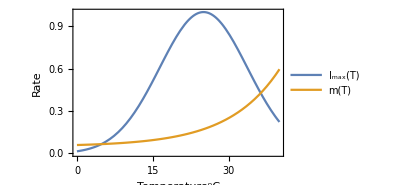
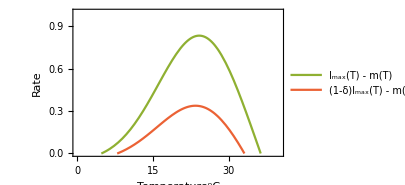

```mathematica
R0=0.5;
e=0.5;
TI=25;
β=150;
Subscript[m, a]=0.01;
Subscript[m, b]=0.1;
Subscript[m, c]=0.05;
uppertval=40;

Column@{Plot[{Imax[T],m[T]},{T,0,uppertval},PlotRange->{0,1}, Frame->{True, True,False,False},FrameLabel->{"Temperature^oC","Rate"},LabelStyle->13,PlotLegends->{"I_max(T)","m(T)"},ImageSize->300],Plot[{ Null,Null,Imax[T]-m[T],e Imax[T]-m[T]},{T,0,uppertval},PlotRange->{0,1}, PlotStyle->{ColorData[97,3],ColorData[97,4]},Frame->{True, True,False,False},FrameLabel->{"Temperature^oC","Rate"},LabelStyle->13,ImageSize->300,PlotLegends->{"I_max(T) - m(T)","(1-δ)I_max(T) - m(T)"}]}
```

#### The following section shows the effect of food concentration on the per capita growth rate of the consumer.

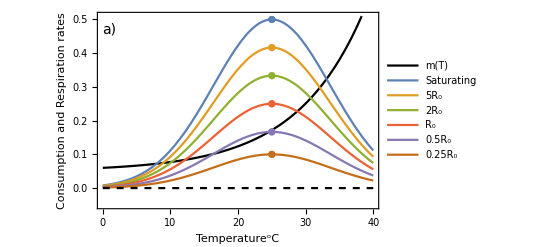

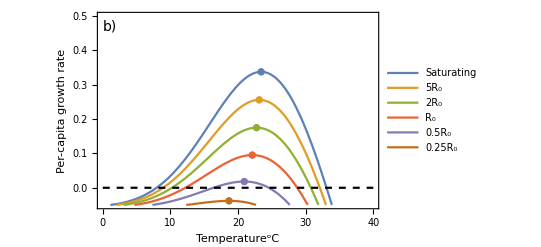

```mathematica
vals=R0 Reverse[{0.25,0.5,1,2,5,10^10}];(* Values of food density to plot *)
maxes=Table[Quiet[FindMaximum[(e Imax[T] R[t]/(R0+R[t]))/.R[t]->x,{T,20}]],{x,vals}];
points=Table[{{T/.maxes[[i,2]],maxes[[i,1]]}},{i,1,Length[maxes]}];

fig1a=Show[Plot[m[T],{T,0,uppertval},PlotStyle->Black,PlotLegends->{"m(T)\n"},Frame->{True,True,False,False},FrameLabel->{"Temperature^oC","Consumption and Respiration rates"},LabelStyle->13,PlotRange->{-.05,.51},Epilog->Inset[Style["a)",14],{1,.47}]],Plot[Evaluate[Table[(e Imax[T] R[t]/(R0+R[t]))/.R[t]->x,{x,vals}]],{T,0,uppertval},PlotLegends->Reverse[{"0.25R_0","0.5R_0","R_0","2R_0","5R_0","Saturating"}]],ListPlot[points],Plot[0,{T,0,uppertval},PlotStyle->{Black,Thin,Dashed}],ImageSize->400]

pcgr=eqC[[2]]/CN[t];
vals=R0 Reverse[{0.25,0.5,1,2,5,10^10}];
maxes=Table[Quiet[FindMaximum[pcgr/.R[t]->x,{T,20}]],{x,vals}];
points=Table[{{T/.maxes[[i,2]],maxes[[i,1]]}},{i,1,Length[maxes]}];
fig1b=Show[Plot[Evaluate[Table[pcgr/.R[t]->x,{x,vals}]],{T,0,uppertval},Frame->{True,True,False,False},FrameLabel->{"Temperature^oC","Per-capita growth rate"},LabelStyle->13,PlotLegends->Reverse[{"0.25R_0","0.5R_0","R_0","2R_0","5R_0","Saturating"}],PlotRange->{-.05,.5},Epilog->Inset[Style["b)",14],{1,.47}]],ListPlot[points],Plot[0,{T,0,uppertval},PlotStyle->{Black,Thin,Dashed}],ImageSize->400]
```

#### Now we will plot this same information in a different manner. We can solve the zero-intercepts of the performance curves above for different levels of resource saturation and plot those. The result is the u-shaped function below,which delimits (in the filled area) what combinations of temperature and resource densities permit positive growth.The optimum temperature as a function of resource density is shown by the dashed line

{{x→ConditionalExpression[(-5.-1. 2.71828^(0.1 T))/(5.-50. 2.71828^(-0.00666667 (-25.+T)^2)+2.71828^(0.1 T)), 7.96057<T<33.084||T>33.084||T<7.96057]}}

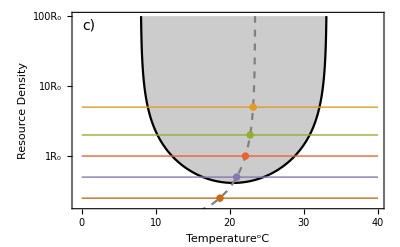

```mathematica
ufunc=Quiet[Solve[0==pcgr/.R[t]->(R0 x),{T,x},Reals]]
upeak=Table[{T/.(Quiet[FindMaximum[{pcgr/.R[t]->R0 x,0<T<40} ,{T,20}]][[2]]),x},{x,10^Range[-1,2,.1]}];
upeakpts=Table[{{T/.(Quiet[FindMaximum[{pcgr/.R[t]->R0 x,0<T<40} ,{T,20}]][[2]]),x}},{x,vals/R0}];
tcks=Join[Flatten[Table[{j*i," "},{j,{.1,1,10,100}},{i,1,9}],1],{{0.1,"0.1R_0"},{.2,""},{.3,""},{1,"1R_0"},{10,"10R_0"},{100,"100R_0"}}];
fig2b=Show[LogPlot[x/.ufunc,{T,0,uppertval},PlotRange->{{-0.5,40},{0.2,100}},Frame->{True,True,False,False},FrameLabel->{"Temperature^oC","Resource Density"},LabelStyle->13,FrameTicks->{Automatic,tcks},PlotStyle->Black,Filling->Top,Epilog->Inset[Style["c)",14],{1,4.3}]],ListLogPlot[upeak,Joined->True,PlotStyle->{Gray,Dashed}],LogPlot[Evaluate[vals/R0],{T,0,40},PlotStyle->{{Thickness[.0025]}}],ListLogPlot[upeakpts],ImageSize->400]
```

### Next we generate plots of the equilibria of the model and the eigenvalues of the Jacobian matrix of the model, assuming that resource dynamics are governed by Chemostat dynamics

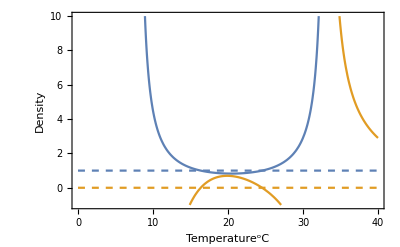
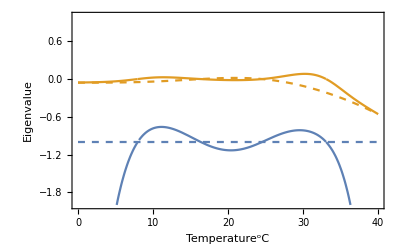

```mathematica
(* Define parameters and equations for the chemostat model *)
Dil=1;
S=1;
R0=2;

eqR:=R'[t]==Dil (S-R[t])- Imax[T]R[t] CN[t]/(R0+R[t]);
eqsol=Solve[{eqR[[2]]==0,eqC[[2]]==0},{R[t],CN[t]}];
eigenvals=Eigenvalues[{{D[eqR[[2]],R[t]],D[eqR[[2]],CN[t]]},{D[eqC[[2]],R[t]],D[eqC[[2]],CN[t]]}}];

Row@{Show[Plot[Evaluate[{R[t],CN[t]}/.eqsol[[2]]],{T,0,uppertval},PlotRange->{-1,10},ImageSize->400,Frame->{True,True,False,False},FrameLabel->{"Temperature^oC","Density"},LabelStyle->13],Plot[Evaluate[{R[t],CN[t]}/.eqsol[[1]]],{T,0,uppertval},PlotRange->{-1,10},PlotStyle->Dashed]],
Show[Plot[Evaluate[eigenvals/.eqsol[[2]]],{T,0,uppertval},PlotRange->{-2Dil,1},ImageSize->400,Frame->{True,True,False,False},FrameLabel->{"Temperature^oC","Eigenvalue"},LabelStyle->13],
Plot[Evaluate[eigenvals/.eqsol[[1]]],{T,0,uppertval},PlotRange->{-Dil-.5,1},PlotStyle->Dashed]]}

(* Blue lines are resource dynamics and orange are consumers, dashed represents (S,0) equilibrium and solid lines are non trivial eqilibrium*)
(* Right panels: Solid lines shows the eigenvalues (blue and orange are #1 and #2) for the non trivial equilibrim and dahsed for the (S,0) equilibrium *)
```

### Here we make a bifurcation plot that shows equilibria and their stability. To do this we discretize the plots into a set of points along the temperature axis - and create two lists, one of the unstable equilibrium points and another of the stable equilibrium points.

First::nofirst: {} has zero length and no first element.

Last::nolast: {} has zero length and no last element.

First::nofirst: {} has zero length and no first element.

Last::nolast: {} has zero length and no last element.

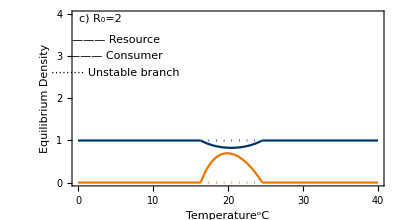

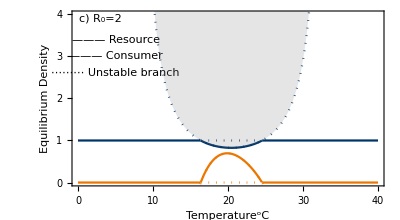

```mathematica
colors={RGBColor["#00356B"],RGBColor["#eb7600"]};
p={Null,Null};
resolution=0.025;
Do[
stable=Table[If[(Evaluate[eigenvals[[2]]/.eqsol[[sol]]]/.T->T)<0&&(Evaluate[eigenvals[[1]]/.eqsol[[sol]]]/.T->T)<0&&
(R[t]/.Evaluate[eqsol[[sol]]/.T->T])≥0,eqsol[[sol]]/.T->T,{R[t]->Nan,CN[t]->Nan}],{T,0,uppertval,resolution}];
unstable=Table[If[(Evaluate[eigenvals[[2]]/.eqsol[[sol]]]/.T->T)>=0||(Evaluate[eigenvals[[1]]/.eqsol[[sol]]]/.T->T)>=0,eqsol[[sol]]/.T->T,{R[t]->Null,CN[t]->Null}],{T,0,uppertval,resolution}];

picks=If[NumberQ[#],If[#>=0,1,0],0]&/@(CN[t]/.unstable);
tvals=Range[0,uppertval,0.025];
CNunstable=Partition[Riffle[Pick[tvals,picks,1],Pick[CN[t]/.unstable,picks,1]],2];
CNunstable={First[CNunstable],Last[CNunstable]};
Runstable=Partition[Riffle[Pick[tvals,picks,1],Pick[R[t]/.unstable,picks,1]],2];
Runstable={First[Runstable],Last[Runstable]};

p[[sol]]=ListPlot[{R[t]/.stable,If[Runstable=={},{Nan,Nan},Runstable],CN[t]/.stable,If[CNunstable=={},{Nan,Nan},CNunstable]},PlotStyle->{{colors[[1]],Automatic},{colors[[1]],Dotted},{colors[[2]],Automatic},{colors[[2]],Dotted}},Joined->True,DataRange->{0,uppertval},Frame->{True,True,False,False},FrameLabel->{"Temperature^oC","Equilibrium Density"},LabelStyle->13,ImageSize->400,Axes->None,AspectRatio->0.55];
,{sol,1,2}];
fig3=Show[p,PlotRange->{{0,uppertval},{0,4}},Epilog->{Inset[Text[Style["c) R_0=2",14]],{3,3.9}],Inset[Text[Style["——— Resource ",12,colors[[1]]]],{5,3.4}],Inset[Text[Style["——— Consumer",12,colors[[2]]]],{5,3.0}],Inset[Text[Style["⋯⋯⋯ Unstable branch",10,Black]],{5,2.6}]}]
out2=Show[fig3,Plot[Evaluate[{R[t],CN[t]}/.eqsol[[2]]],{T,8,33},PlotStyle->{{colors[[1]],Dotted},{colors[[2]],Dotted}},Filling->{1->{Top,Directive[Gray,Opacity[0.2]]},2->None}]]
```

#### Below is a plot of the consumer turnover rate vs. temperature, given as the production/biomass ratio

```mathematica
A reasonable question here is - what makes the equilibirum relationship so skewed relative to the underlying performance curves.  In part this is due to the  shifting optimum - shown below; however this is not the entire explanation.   Turnover also plays an important role.  At low temperatures biomass turnover is much less smaller while at warmer temperatures, turnover is much greater, leading to greater losses of energy in the non-assimilated fraction of biomass.  In addition, there is a greater maintenance cost at higher teperatures, which is reflected in the locations of CTmin and CTmax on the performance curve.
```

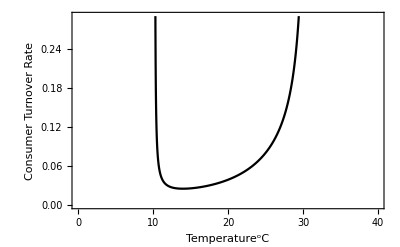

```mathematica
pbratio=Table[(eqC[[2,2,3]]/CN[t])/.stable[[i]]/.T->(resolution*i),{i,1,Length[stable]}];
fig4=ListPlot[pbratio,PlotStyle->Black,Joined->True,DataRange->{0,uppertval},Frame->{True,True,False,False},FrameLabel->{"Temperature^oC","Consumer Turnover Rate"},LabelStyle->13,ImageSize->400,Axes->None,PlotRange->{{0,uppertval},Automatic}]
```

#### Next we look at a similar analysis but for a logistically growing resource. Note that continuing requires a refresh of the kernel (or clearing of variable definitions as some are redefined in a different context )

```mathematica
(* Quit the kernel and repeat for a logistically growing resource *)
(* Define all the necessary functions, equations and solutions for equilibirum and eigenvalues *)

r[T_]:=br Exp[-((T-(TI+δT))^2)/β]-(d1 Exp[d2 T]+d3);
k[T_]:=r[T]/γ;
Imax[T_]:=Exp[-((T-TI)^2)/β];
m[T_]:=ma Exp[mb T]+mc;

eqR:=R'[t]==r[T]R[t](1-R[t]/k[T])- Imax[T]R[t] CN[t]/(R0+R[t]);
eqC:=CN'[t]==CN[t](e Imax[T] R[t]/(R0+R[t])-m[T]);

eqsol=Solve[{eqR[[2]]==0,eqC[[2]]==0},{R[t],CN[t]}];

eigenvals=Eigenvalues[{{D[eqR[[2]],R[t]],D[eqR[[2]],CN[t]]},{D[eqC[[2]],R[t]],D[eqC[[2]],CN[t]]}}];
```

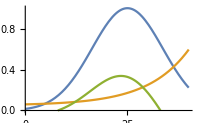
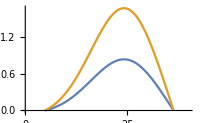
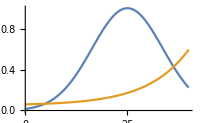

```mathematica
(* Define the standar set of parameters and generate a few prelimiary plots of vital functions*)
br=1;
d1=0.01;
d2=0.1;
d3=0.05;
γ=0.5;
R0=1;
β=150;
e=0.5;
δT=0; (* thermal Mismatch parameter -- Important *)
TI=25;
β=150;
ma=0.01;
mb=0.1;
mc=0.05;
uppertval=40;
Row@{Plot[{Imax[T],m[T],e Imax[T]-m[T]},{T,0,uppertval},PlotRange->{0,1},ImageSize->200,PlotLegends->{"Imax","m","Max p.c. gr"}],Plot[{r[T],k[T]},{T,0,uppertval},PlotRange->{0,Automatic},ImageSize->200,PlotLegends->{"r","K"}],
Plot[{br Exp[-((T-(TI+δT))^2)/β],(d1 Exp[d2 T]+d3)},{T,0,uppertval},PlotRange->{0,Automatic},ImageSize->200,PlotLegends->{"b","d"}]}
```

#### Next we generate plots of the equilibria of the model and the eigenvalues of the Jacobian matrix of the model,assuming that resource dynamics are governed by the Logistic Model. To do this we discretize the plots into a set of points along the temperature axis-and create two lists,one of the unstable equilibrium points and another of the stable equilibrium points. Because there are imaginary parts of some of the eigenvalues, we also plot the fluctuation amplitudes

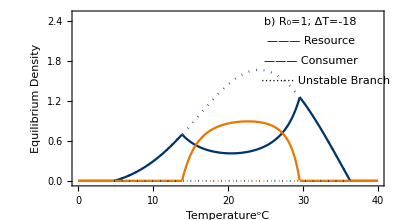

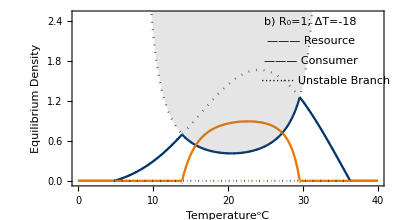

```mathematica
colors={RGBColor["#00356B"],RGBColor["#eb7600"]};
p={Null,Null,Null};
resolution=0.025;
stable={1,1,1};
unstable={1,1,1};
Do[
stable[[sol]]=Table[If[(Re[Evaluate[eigenvals[[2]]/.eqsol[[sol]]]/.T->T])<0&&(Re[Evaluate[eigenvals[[1]]/.eqsol[[sol]]]/.T->T])<0&&
(R[t]/.Evaluate[eqsol[[sol]]/.T->T])≥0,(*negative resource vals wouldn't make sense*)
eqsol[[sol]]/.T->T,
{R[t]->Nan,CN[t]->Nan}],(*if not true, Nan in table*)
{T,0,uppertval,resolution}];

p[[sol]]=ListPlot[{R[t]/.stable[[sol]],CN[t]/.stable[[sol]]},

PlotStyle->{{colors[[1]],Automatic},
{colors[[2]],Automatic}},
Joined->True,DataRange->{0,uppertval},Frame->{True,True,False,False},
FrameLabel->{"Temperature^oC","Equilibrium Density"},LabelStyle->13,ImageSize->400,Axes->None,PlotRange->{-0.025,2.5},AspectRatio->0.55],

{sol,1,3}];
over=25;
mainp=Show[p,Epilog->{Inset[Text[Style["b) R_0=1; ΔT=-18",14]],{6+over,2.4}],Inset[Text[Style["——— Resource ",12,colors[[1]]]],{6+over,2.1}],Inset[Text[Style["——— Consumer",12,colors[[2]]]],{6+over,1.8}],Inset[Text[Style["⋯⋯⋯ Unstable Branch",12,Black]],{7.95+over,1.5}]},PlotRange->{{0,40},{-0.025,2.5}}] ;(*limit cycles in center range. transitions between equilibrium points are the interesting points (transcritical bifurcations)*) (*maybe layer on numerical simulations for the amplitude of the cycles*)
amplitudes=Table[
Module[{sol,Rsize,Csize},
sol=NDSolve[{eqR/.T->i,eqC/.T->i,R[0]==5,CN[0]==.1},{R,CN},{t,0,1000}];
Csize=Table[CN[t]/.sol,{t,800,1000,0.1}];
Rsize=Table[R[t]/.sol,{t,800,1000,0.1}];
{i,Min[Rsize],Max[Rsize],Min[Csize],Max[Csize]}],{i,5,35,.1}];
flucp=ListLinePlot[Table[amplitudes[[1;;,{1,i}]],{i,2,5}],
PlotStyle->{{colors[[1]],Opacity[.02]},{colors[[1]],Opacity[.02]},{colors[[2]],Opacity[.02]},{colors[[2]],Opacity[.02]}},
Filling->{1->{2},3->{4}}];
out=Show[mainp,flucp,Plot[If[k[T]>=0,k[T],Null],{T,0,40},PlotStyle->{{colors[[1]],Dotted}}],Plot[0,{T,0.3,40},PlotStyle->{{colors[[2]],Dotted}}],Plot[If[k[T]>0,0,Null],{T,0,40},PlotStyle->{{colors[[1]],Dotted}}]]
(*Below is just for the limit cycle solutions *)
out2=Show[out,Plot[Evaluate[{R[t],CN[t]}/.eqsol[[3]]],{T,8,33},PlotStyle->{{colors[[1]],Dotted},{colors[[2]],Dotted}},Filling->{1->{Top,Directive[Gray,Opacity[0.2]]},2->None},PlotRange->Full]]
```

#### Next we generate a plot looking at the effect of thermal mismatch on the consumer’s per-capita growth rate. The contours show different values and describe how the thermal performace curve changes along a second dimension (thermal mismatch)

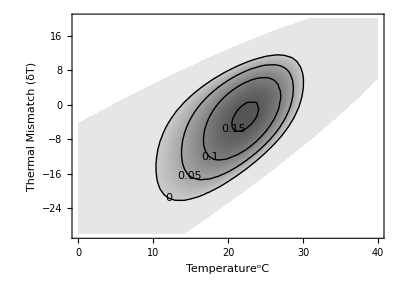

```mathematica
Clear[δT];
colfcn[x_]:=Blend[{Lighter[Gray,0.6],Darker[Gray]},x];
colfcnb[x_]:=If[x<0,White,Gray];
asymplot=Show[ContourPlot[k[T],{T,0,40},{δT,-30,20},Contours->{0},ContourStyle->None,ContourShading->{White,Lighter[Gray,0.8]},Frame->{True,True,False,False},AspectRatio->1/Sqrt[2],FrameLabel->{"Temperature^oC","Thermal Mismatch (δT)"}, FrameStyle->13,FrameTicksStyle->12],ContourPlot[eqC[[2]]/CN[t]/.R[t]->k[T],{T,0,35},{δT,-30,20},PlotRange->{0,Automatic},ColorFunction->colfcn,Contours->100,ContourStyle->None],ContourPlot[eqC[[2]]/CN[t]/.R[t]->k[T],{T,0,35},{δT,-30,20},
ContourShading->None,Contours->{0,0.05,.1,.15},ContourLabels->All]]
```

#### Last, we show a number of sections through the above plot, first by plotting all the TPCs on one plot, and then by separating them into distinct curves as shown in figure 4 of the paper.

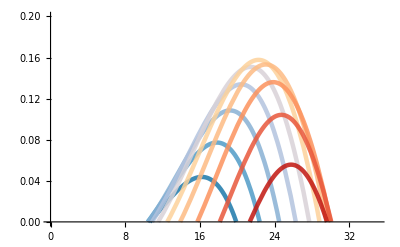

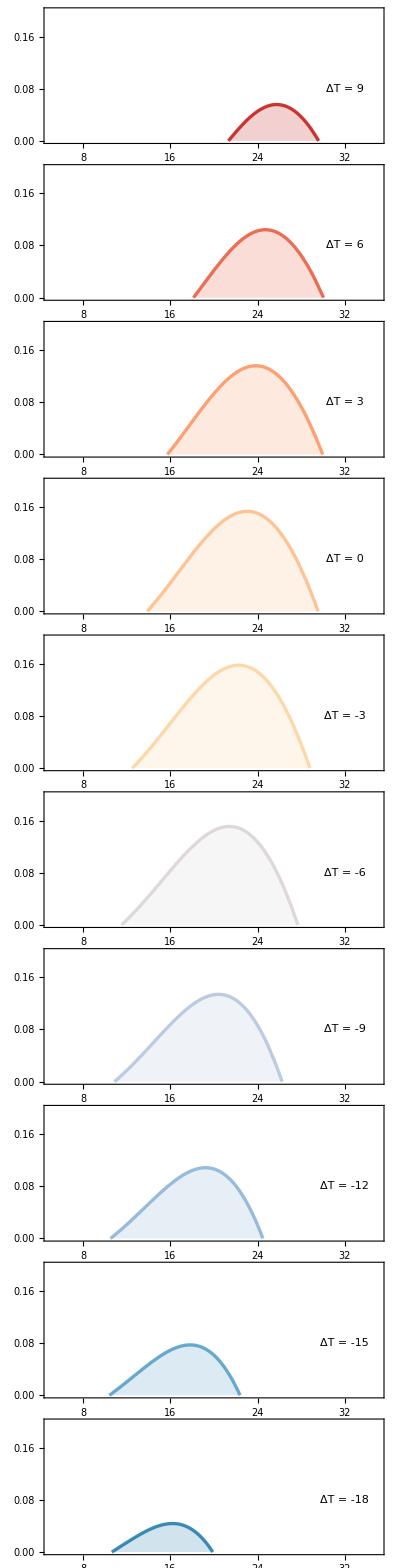

```mathematica
dtr=Range[-18,9,3];
curves=Table[eqC[[2]]/CN[t]/.R[t]->k[T],{δT,dtr}];
cfunction[x_]:=Blend[{RGBColor["#045a8d"],RGBColor["#2b8cbe"],RGBColor["#74a9cf"],RGBColor["#a6bddb"],RGBColor["#d0d1e6"],RGBColor["#fdd49e"],RGBColor["#fdbb84"],RGBColor["#fc8d59"],RGBColor["#e34a33"],RGBColor["#b30000"]},x];
colors=Table[{Directive[cfunction[(δT+20)/30],Thickness[0.008],Opacity[0.85]]},{δT,dtr}];
Plot[Evaluate[curves],{T,0,35},PlotRange->{0,0.2},PlotStyle->colors]


Column[Table[Plot[curves[[i]],{T,0,35},PlotRange->{{5,35},{0,0.2}},PlotStyle->colors[[i]],AspectRatio->.2,Ticks->None,Background->None,ImageSize->300,Filling->Axis,Frame->{True,True,False,False},Axes->{0,None},FrameTicks->None,FrameStyle->Thickness[0.005],Epilog->Inset[Text[Style["ΔT = "<>ToString[dtr[[i]]],14]],{32,.08}]],{i,Length[curves],1,-1}],Spacings->-.25]
```